```mathematica
Clear["Global`*"]
(* k ~ 0 the thermal conductivity*)
```

```mathematica
Subscript[κ, E] = (T/Subscript[v, s]^2)^2 *((Subscript[v, t]*Sin[ϕ]*(h+3*Subscript[v, s])^2)/(6 √3*Pi))*(PolyLog[3, (E^(-h/T))]);
```

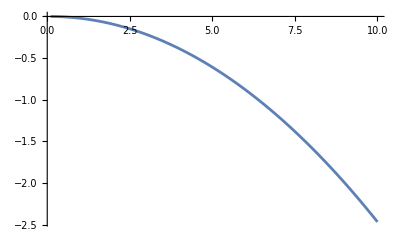

```mathematica
Plot[Subscript[κ, E]/.{Subscript[v, s]->1,h ->0.1,  Subscript[v, t]->-0.1, ϕ->Pi/4}, {T, 0.1, 10}]
```

```mathematica
(* J1 magnon*)
a1 = {1/2, √3/2}; a2 = {1/2, -√3/2}; a3= {-1,0 };
b1 = {0, -√3}; b2 = {3/2, √3/2}; b3 = {-3/2,√3/2 };
k = {kx, ky};
fk = 2*(Sin[k.b1] + Sin[k.b2] + Sin[k.b3]); 
gk = E^(-I *k.a1) + E^(-I*k.a2) +E^(-I*k.a3);
gkk = E^(I *k.a1) + E^(I*k.a2) +E^(I*k.a3);
H = {{ -3*J1 + d1*fk, J1 * gk}, {J1 * gkk, -3J1 - d1*fk}};
test = H/.{J1->-1, d1->0.0, kx->0, ky->0}
```

{{3.,-3},{-3,3.}}

```mathematica
(*Plot3D[ Eigenvalues[H/.{J1->-1, D->0}], {kx, -2*Pi, 2*Pi}, {ky, -2*Pi, 2*Pi}]*)
```

```mathematica
Eigenvalues[test]//Simplify
```

{6.,0.}

```mathematica
Subscript[ϕ, 1]=Eigenvectors[H/.{J1->-1, d1->-0.1}, 1][[1]]//Simplify; 
Subscript[ϕ, 1]
```

{(-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx-0.866025 ky]+0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx+0.866025 ky]-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.73205 ky]+0.5 √(4. ⅇ^((0.+2. ⅈ) kx)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+12. ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2+ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (-0.32 Sin[1.5 kx+0.866025 ky]+0.32 Sin[1.73205 ky])-0.32 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2))/(ⅇ^((0.+1.5 ⅈ) kx)+ⅇ^((0.+1.5 ⅈ) kx+(0.+1.73205 ⅈ) ky)+ⅇ^((0.+0.866025 ⅈ) ky)),1.}

```mathematica
Subscript[Ω, 1]=-I *(Im[D[Subscript[ϕ, 1], kx]] . D[Subscript[ϕ, 1], ky] ) //Simplify;
```

```mathematica
Plot3D[Subscript[Ω, 1], {kx, -6, 6}, {ky, -6, 6}]
```

-Graphics3D-

```mathematica
Plot3D[ Eigenvalues[H/.{J1->-1, d1->0}], {kx, -2*Pi, 2*Pi}, {ky, -2*Pi, 2*Pi}]
```

-Graphics3D-

```mathematica
Subscript[Ω, 1]
```

-((ⅈ Conjugate[-ⅇ^((0.+1.5 ⅈ) kx) ((0.+1.5 ⅈ)+(0.+1.5 ⅈ) ⅇ^((0.+1.73205 ⅈ) ky)) (-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx-0.866025 ky]+0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx+0.866025 ky]-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.73205 ky]+0.5 √(4. ⅇ^((0.+2. ⅈ) kx)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+12. ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2+ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (-0.32 Sin[1.5 kx+0.866025 ky]+0.32 Sin[1.73205 ky])-0.32 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2))+(ⅇ^((0.+1.5 ⅈ) kx)+ⅇ^((0.+1.5 ⅈ) kx+(0.+1.73205 ⅈ) ky)+ⅇ^((0.+0.866025 ⅈ) ky)) (-0.3 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Cos[1.5 kx-0.866025 ky]+0.3 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Cos[1.5 kx+0.866025 ky]-(0.+0.2 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx-0.866025 ky]+(0.+0.2 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx+0.866025 ky]-(0.+0.2 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.73205 ky]+(0.25 ((0.+8. ⅈ) ⅇ^((0.+2. ⅈ) kx)+(0.+2. ⅈ) ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+(0.+14. ⅈ) ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+(0.+24. ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+(0.+2. ⅈ) ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+(0.+14. ⅈ) ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+(0.+8. ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.24 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[3. kx-1.73205 ky]-0.48 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Cos[1.5 kx+0.866025 ky] Sin[1.5 kx-0.866025 ky]+(0.+0.32 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+(0.+0.32 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2-0.48 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Cos[1.5 kx-0.866025 ky] (1. Sin[1.5 kx+0.866025 ky]-1. Sin[1.73205 ky])-(0.+0.64 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (1. Sin[1.5 kx+0.866025 ky]-1. Sin[1.73205 ky])-0.48 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Cos[1.5 kx+0.866025 ky] Sin[1.73205 ky]-(0.+0.64 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+(0.+0.32 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2+0.24 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[3. kx+1.73205 ky]))/(√(4. ⅇ^((0.+2. ⅈ) kx)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+12. ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2+ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (-0.32 Sin[1.5 kx+0.866025 ky]+0.32 Sin[1.73205 ky])-0.32 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2)))] ((ⅇ^((0.+1.5 ⅈ) kx)+ⅇ^((0.+1.5 ⅈ) kx+(0.+1.73205 ⅈ) ky)+ⅇ^((0.+0.866025 ⅈ) ky)) (0.173205 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Cos[1.5 kx-0.866025 ky]+0.173205 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Cos[1.5 kx+0.866025 ky]-0.34641 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Cos[1.73205 ky]-(0.+0.173205 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx-0.866025 ky]+(0.+0.173205 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx+0.866025 ky]-(0.+0.173205 ⅈ) ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.73205 ky]+((0.-0.034641 ⅈ) ⅇ^((0.+2. ⅈ) kx-(0.+0.866025 ⅈ) ky) (1.+1. ⅇ^((0.+1.73205 ⅈ) ky)+3. ⅇ^((0.+3.4641 ⅈ) ky)-5. ⅇ^((0.+5.19615 ⅈ) ky)) Cos[(1.5+0. ⅈ) kx]+ⅇ^((0.+2. ⅈ) kx) ((0.+0.069282 ⅈ) ⅇ^((0.+1.73205 ⅈ) ky)-(0.+0.069282 ⅈ) ⅇ^((0.+3.4641 ⅈ) ky)) Cos[(1.5+0. ⅈ) kx]^2+ⅇ^((0.-1.73205 ⅈ) ky) ((0.+0.0173205 ⅈ) ⅇ^((0.+2. ⅈ) kx)+(0.+0.866025 ⅈ) ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+(0.+0.866025 ⅈ) ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+(0.+5.30008 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+(0.+2.59808 ⅈ) ⅇ^((0.+0.5 ⅈ) kx+(0.+4.33013 ⅈ) ky)+(0.+2.59808 ⅈ) ⅇ^((0.+3.5 ⅈ) kx+(0.+4.33013 ⅈ) ky)+(0.+3.39482 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+5.19615 ⅈ) ky)-(0.+0.0519615 ⅈ) ⅇ^((0.+2. ⅈ) kx+(0.+6.9282 ⅈ) ky)+ⅇ^((0.+2. ⅈ) kx) ((0.-0.069282 ⅈ) ⅇ^((0.+3.4641 ⅈ) ky)+(0.+0.069282 ⅈ) ⅇ^((0.+5.19615 ⅈ) ky)) Sin[(1.5+0. ⅈ) kx]^2))/(√(4. ⅇ^((0.+2. ⅈ) kx)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+12. ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2+ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (-0.32 Sin[1.5 kx+0.866025 ky]+0.32 Sin[1.73205 ky])-0.32 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2)))-((0.+1.73205 ⅈ) ⅇ^((0.+1.5 ⅈ) kx+(0.+1.73205 ⅈ) ky)+(0.+0.866025 ⅈ) ⅇ^((0.+0.866025 ⅈ) ky)) (-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx-0.866025 ky]+0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.5 kx+0.866025 ky]-0.2 ⅇ^((0.+1. ⅈ) kx+(0.+0.866025 ⅈ) ky) Sin[1.73205 ky]+0.5 √(4. ⅇ^((0.+2. ⅈ) kx)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+0.866025 ⅈ) ky)+12. ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky)+4. ⅇ^((0.+0.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+3.5 ⅈ) kx+(0.+2.59808 ⅈ) ky)+4. ⅇ^((0.+2. ⅈ) kx+(0.+3.4641 ⅈ) ky)+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky]^2+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky]^2+ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx-0.866025 ky] (-0.32 Sin[1.5 kx+0.866025 ky]+0.32 Sin[1.73205 ky])-0.32 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.5 kx+0.866025 ky] Sin[1.73205 ky]+0.16 ⅇ^((0.+2. ⅈ) kx+(0.+1.73205 ⅈ) ky) Sin[1.73205 ky]^2))))/((ⅇ^((0.+1.5 ⅈ) kx)+ⅇ^((0.+1.5 ⅈ) kx+(0.+1.73205 ⅈ) ky)+ⅇ^((0.+0.866025 ⅈ) ky))^2 (ⅇ^((0.-1.5 ⅈ) Conjugate[kx])+ⅇ^((0.-1.5 ⅈ) Conjugate[kx]-(0.+1.73205 ⅈ) Conjugate[ky])+ⅇ^((0.-0.866025 ⅈ) Conjugate[ky]))^2))

```mathematica
a = {1+I, 2};
b = {1+I, 2}; 
Conjugate[a]
```

{1-ⅈ,2}